```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
v2mColor=Purple;
```

```mathematica
(****V1 to V2m******)
```

```mathematica
dateMouseSessionList={{"082120","Mouse21060","Session2"},{"082220","Mouse21060","Session3"},{"082320","Mouse21060","Session2"},{"082520","Mouse21060","Session2"},{"090820","Mouse21067","Session2"},{"101720","Mouse23392","Session1"},{"101520","Mouse23393","Session2"},{"101420","Mouse23395","Session2"},{"121020","Mouse23379","Session1"},{"121520","Mouse23365","Session2"},{"122020","Mouse23365","Session1"},{"121520","Mouse23379","Session2"},{"121920","Mouse23379","Session1"},{"020421","Mouse23320","Session1"},{"020421","Mouse23329","Session1"},{"022721","Mouse23329","Session1"},{"030621","Mouse23329","Session1"},{"071721","Mouse21108","Session1"}};
```

```mathematica
(***Extract all the ROIs for this particular stimulus type***)
```

```mathematica
allROIsPerSession=Table[Range@Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/dFOverF0TimeSeries/"]]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
discardROIsList=Table[Flatten@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","discardROIs",".txt"],"List"]),{n,1,Length[dateMouseSessionList]}];
```

```mathematica
allROIsPerSession=Table[Complement[allROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[allROIsPerSession]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","sigResponsiveROIs.txt"],"List"],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Complement[sigRespGratingsROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[sigRespGratingsROIsPerSession]}];
```

```mathematica
nonSigROIsPerSession=Table[Complement[allROIsPerSession[[n]],sigRespGratingsROIsPerSession[[n]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
(***Extract all the visual responses for the ROIs extracted***)
```

```mathematica
visRespGratingsV1toV2m=Abs/@DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,sigRespGratingsROIsPerSession[[n]]}],{n,1,Length[sigRespGratingsROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespNonRespV1toV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,nonSigROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespAllV1toV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,allROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
(****LM to V2m******)
```

```mathematica
dateMouseSessionList={{"092221","Mouse22422","Session1"},{"100421","Mouse22422","Session1"},{"081221","Mouse22437","Session2"},{"081521","Mouse22437","Session1"},{"082021","Mouse22437","Session1"},{"082421","Mouse22437","Session1"},{"092321","Mouse22472","Session1"},{"101021","Mouse22472","Session1"},{"081921","Mouse22491","Session1"},{"102021","Mouse22422","Session1"},{"102121","Mouse22436","Session1"},{"102221","Mouse22472","Session1"},{"071522","Mouse23025","Session1"},{"071222","Mouse23100","Session2"},{"071122","Mouse23014","Session1"},{"070822","Mouse22518","Session1"},{"071022","Mouse22518","Session1"}};
```

```mathematica
(***Extract all the ROIs for this particular stimulus type***)
```

```mathematica
allROIsPerSession=Table[Range@Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/dFOverF0TimeSeries/"]]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
discardROIsList=Table[Flatten@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","discardROIs",".txt"],"List"]),{n,1,Length[dateMouseSessionList]}];
```

```mathematica
allROIsPerSession=Table[Complement[allROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[allROIsPerSession]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","sigResponsiveROIs.txt"],"List"],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Complement[sigRespGratingsROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[sigRespGratingsROIsPerSession]}];
```

```mathematica
nonSigROIsPerSession=Table[Complement[allROIsPerSession[[n]],sigRespGratingsROIsPerSession[[n]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
(***Extract all the visual responses for the ROIs extracted***)
```

```mathematica
visRespGratingsLMtoV2m=Abs/@DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,sigRespGratingsROIsPerSession[[n]]}],{n,1,Length[sigRespGratingsROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespNonRespLMtoV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,nonSigROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespAllLMtoV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,allROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
(****LP to V2m******)
```

```mathematica
dateMouseSessionList={{"102020","Mouse23394","Session2"},{"102320","Mouse23394","Session1"},{"100720","Mouse23399","Session2"},{"101020","Mouse23399","Session2"},{"110120","Mouse23394","Session2"},{"103120","Mouse23378","Session2"},{"110320","Mouse23378","Session1"},{"110120","Mouse23377","Session1"},{"111620","Mouse23384","Session1"},{"111720","Mouse23384","Session3"},{"112020","Mouse23384","Session2"},{"120420","Mouse23378","Session1"},{"120220","Mouse23378","Session2"},{"120420","Mouse23384","Session1"},{"120220","Mouse23384","Session2"},{"121620","Mouse23381","Session2"},{"121920","Mouse23381","Session1"},{"011221","Mouse23369","Session1"},{"011521","Mouse23369","Session2"},{"010721","Mouse23339","Session1"},{"011521","Mouse23339","Session1"},{"030921","Mouse23339","Session1"},{"031121","Mouse23369","Session1"},{"070122","Mouse23067","Session1"},{"071122","Mouse23075","Session1"}};
```

```mathematica
(***Extract all the ROIs for this particular stimulus type***)
```

```mathematica
allROIsPerSession=Table[Range@Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/dFOverF0TimeSeries/"]]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
discardROIsList=Table[Flatten@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","discardROIs",".txt"],"List"]),{n,1,Length[dateMouseSessionList]}];
```

```mathematica
allROIsPerSession=Table[Complement[allROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[allROIsPerSession]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","sigResponsiveROIs.txt"],"List"],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Complement[sigRespGratingsROIsPerSession[[n]],discardROIsList[[n]]],{n,1,Length[sigRespGratingsROIsPerSession]}];
```

```mathematica
nonSigROIsPerSession=Table[Complement[allROIsPerSession[[n]],sigRespGratingsROIsPerSession[[n]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
(***Extract all the visual responses for the ROIs extracted***)
```

```mathematica
visRespGratingsLPtoV2m=Abs/@DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,sigRespGratingsROIsPerSession[[n]]}],{n,1,Length[sigRespGratingsROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespNonRespLPtoV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,nonSigROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespAllLPtoV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,allROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
(****V2m******)
```

```mathematica
dateMouseSessionList={{"090820","Mouse21011","Session2"},{"092620","Mouse21011","Session1"},{"091520","Mouse21069","Session2"},{"112020","Mouse23383","Session2"},{"112120","Mouse23383","Session2"},{"112220","Mouse23386","Session1"},{"120520","Mouse23383","Session2"},{"010121","Mouse23382","Session1"},{"011521","Mouse23390","Session2"},{"011821","Mouse23390","Session2"},{"021221","Mouse23359","Session2"},{"021821","Mouse23310","Session1"},{"030221","Mouse23310","Session1"},{"031121","Mouse23310","Session1"},{"021721","Mouse23338","Session1"},{"022621","Mouse23338","Session1"},{"030221","Mouse23338","Session1"},{"031521","Mouse23338","Session2"},{"031921","Mouse23338","Session1"},{"072421","Mouse21151","Session2"},{"080121","Mouse22481","Session1"},{"072521","Mouse21133","Session1"},{"072121","Mouse21170","Session1"}};
```

```mathematica
(***Extract all the ROIs for this particular stimulus type***)
```

```mathematica
allROIsPerSession=Table[Range@Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/dFOverF0TimeSeries/"]]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
sigRespGratingsROIsPerSession=Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","sigResponsiveROIs.txt"],"List"],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
nonSigROIsPerSession=Table[Complement[allROIsPerSession[[n]],sigRespGratingsROIsPerSession[[n]]],{n,1,Length[dateMouseSessionList]}];
```

```mathematica
(***Extract all the visual responses for the ROIs extracted***)
```

```mathematica
visRespGratingsV2m=Abs/@DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,sigRespGratingsROIsPerSession[[n]]}],{n,1,Length[sigRespGratingsROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespNonRespV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,nonSigROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
visRespAllV2m=DeleteCases[Flatten@Table[Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionList[[n,1]],"/",dateMouseSessionList[[n,2]],"/",dateMouseSessionList[[n,3]],"/VisStimResults/",dateMouseSessionList[[n,1]],"_",dateMouseSessionList[[n,2]],"_",dateMouseSessionList[[n,3]],"_","overallVisResponse_ZDFF",ToString[roi],".txt"],"List"],{roi,allROIsPerSession[[n]]}],{n,1,Length[nonSigROIsPerSession]}],_?(Not@*NumericQ)];
```

```mathematica
(**********************)
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[visRespAllV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{{-0.6,2},{-4,10}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[visRespAllV1toV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[visRespAllLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{{-0.6,2},{-4,10}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[visRespAllLMtoV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[visRespAllLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{{-0.6,2},{-4,10}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[visRespAllLPtoV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v2mAxonCharts=Show[BoxWhiskerChart[visRespAllV2m,{{"Whiskers", Directive[Darker@v2mColor,Thick]}, {"Fences", Directive[Darker@v2mColor,Thick]},{"MedianMarker", Directive[Darker@v2mColor,Thickness[0.009]]}},PlotRange->{{-0.6,2},{-4,10}},ChartStyle->Directive[v2mColor,Opacity[0.3]],Frame->False],DistributionChart[visRespAllV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v2mColor],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[visRespAllV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{{-0.64,2.0},{-4,10}},ChartStyle->Transparent,Frame->False],DistributionChart[visRespAllV2m,PlotRange->{{-0.5,0.9},{-4,10}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-4,10,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

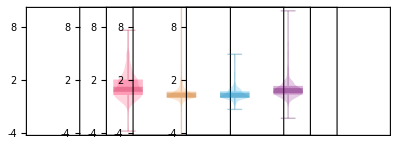

```mathematica
g=GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,v2mAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}},ImageSize->400]
```

```mathematica
PieChart[{Length[visRespNonRespV1toV2m],Length[visRespAllV1toV2m]-Length[visRespNonRespV1toV2m]},ChartBaseStyle->EdgeForm[{Thick,Black}],ChartStyle->{Lighter[v1Color,0.8],v1Color}]
```

-Graphics-

```mathematica
PieChart[{Length[visRespNonRespLMtoV2m],Length[visRespAllLMtoV2m]-Length[visRespNonRespLMtoV2m]},ChartBaseStyle->EdgeForm[{Thick,Black}],ChartStyle->{Lighter[lmColor,0.8],lmColor}]
```

-Graphics-

```mathematica
PieChart[{Length[visRespNonRespLPtoV2m],Length[visRespAllLPtoV2m]-Length[visRespNonRespLPtoV2m]},ChartBaseStyle->EdgeForm[{Thick,Black}],ChartStyle->{Lighter[lpColor,0.8],lpColor}]
```

-Graphics-

```mathematica
PieChart[{Length[visRespNonRespV2m],Length[visRespAllV2m]-Length[visRespNonRespV2m]},ChartBaseStyle->EdgeForm[{Thick,Black}],ChartStyle->{Lighter[v2mColor,0.8],v2mColor}]
```

-Graphics-